## Execute this

### Loading

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
polar1bt=Import["data/polarValArray_b2t.mx"];
polar1tb=Import["data/polarValArray_t2b.mx"];
```

```mathematica
deltaPphip=Flatten[polar1bt,1];
tempPLUS=Flatten[polar1bt,1];
tempMINUS=Flatten[polar1tb,1];
Table[deltaPphip[[i,3]]=tempPLUS[[i,3]]-tempMINUS[[i,3]],{i,1,Length@deltaPphip}];
```

### Plotting

individual sweeps

```mathematica
min=-0.0;
max=1.0;
colormap={"DeepSeaColors","Reverse"};
colfunc=ColorData[colormap][#/max]&;
legPPLUS=BarLegend[{colfunc,{min,max}},LegendLabel->"P_+"];
legPMINUS=BarLegend[{colfunc,{min,max}},LegendLabel->"P_-"];
legNPLUS=BarLegend[{colfunc,{min,max}},LegendLabel->"N_+"];
legNMINUS=BarLegend[{colfunc,{min,max}},LegendLabel->"N_-"];
polplotbt=ListDensityPlot[Flatten[polar1bt,1],InterpolationOrder->0,PlotRange->{All,All,{min,max}},ClippingStyle->{ColorData[colormap][0],ColorData[colormap][1]},ColorFunction->(ColorData[colormap][Rescale[#,{min,max}]]&),ColorFunctionScaling->False,PlotLegends->legPPLUS,FrameLabel->{"α","φ_p"}];
polplottb=ListDensityPlot[Flatten[polar1tb,1],InterpolationOrder->0,PlotRange->{All,All,{min,max}},ClippingStyle->{ColorData[colormap][0],ColorData[colormap][1]},ColorFunction->(ColorData[colormap][Rescale[#,{min,max}]]&),ColorFunctionScaling->False,PlotLegends->legPMINUS,FrameLabel->{"α","φ_p"}];
GraphicsRow[{polplotbt,polplottb},ImageSize->600]
```

-Graphics-

hysteresis

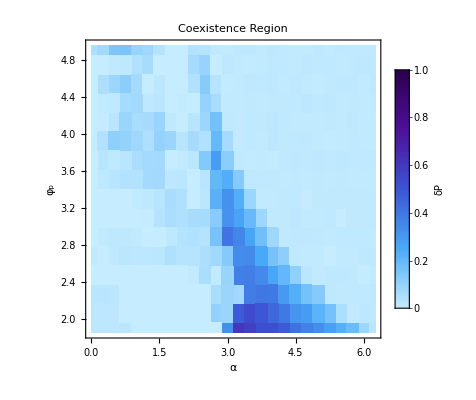

```mathematica
min=-0.01;
max=1.;
colormap={"DeepSeaColors","Reverse"};
colfunc=ColorData[colormap][#/max]&;
leg=BarLegend[{colfunc,{min,max}},LegendLabel->"δP"];
ListDensityPlot[deltaPphip,InterpolationOrder->0,PlotLabel->Style["Coexistence Region",14],PlotRange->{All,All,{min,max}},ClippingStyle->{ColorData[colormap][0],ColorData[colormap][1]},ColorFunction->(ColorData[colormap][Rescale[#,{min,max}]]&),ColorFunctionScaling->False,PlotLegends->leg,FrameLabel->{"α","φ_p"}]
```